```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/marco/Documents/università/D6/notebooks/1310.4838/OeW/nutauWH - self

```mathematica
<<tautauHW0gen_tree.m
```

FeynArts 3.9

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

last revised 2 Dec 14

loading generic model file /Users/marco/FeynArts/FeynArts/Models/Mine/1310.4838.LR.gen

> $GenericMixing is OFF

generic model {Mine/1310.4838.LR} initialized

loading classes model file /Users/marco/FeynArts/FeynArts/Models/Mine/1310.4838.LR.mod

> 64 particles (incl. antiparticles) in 35 classes

> $CounterTerms are ON

> 3391 vertices

classes model {Mine/1310.4838.LR} initialized

Excluding 1 Generic, 10 Classes, and 10 Particles fields

Excluding 2 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 1 Particles insertion

Restoring 1 Generic, 10 Classes, and 10 Particles fields

Restoring 2 field point(s)

in total: 1 Particles insertion

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

amplitudes created

File written

inserting at level(s) {Particles}

> Top. 1: 1 Particles insertion

in total: 1 Particles insertion

> Top. 1: 1 diagram

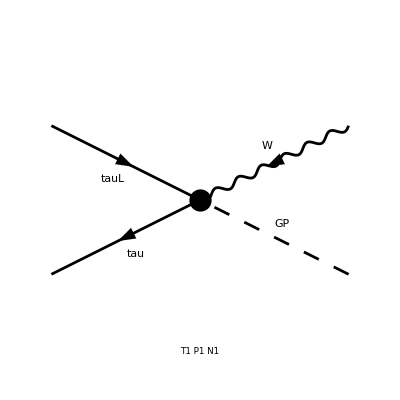

```mathematica
top=CreateTopologies[0,2->2,Adjacencies->{3,4},ExcludeTopologies->{Internal,Tadpoles}];
ins1=InsertFields[top,{F[6],-F[15]}->{-V[3],S[3]},Model->"Mine/1310.4838.LR",GenericModel->"Mine/1310.4838.LR",InsertionLevel->{Particles}];Paint[ins1,ColumnsXRows->{3,1}];
```

inserting at level(s) {Particles}

> Top. 1: 1 Particles insertion

in total: 1 Particles insertion

> Top. 1: 1 diagram

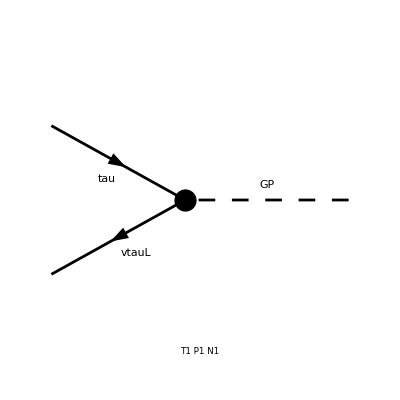

```mathematica
top2=CreateTopologies[0,2->1,Adjacencies->{3,4},ExcludeTopologies->{Internal,Tadpoles}];
ins2=InsertFields[top2,{F[15],-F[3]}->{-S[3]},Model->"Mine/1310.4838.LR",GenericModel->"Mine/1310.4838.LR",InsertionLevel->{Particles}];
Paint[ins2,ColumnsXRows->{3,1}];
```

inserting at level(s) {Particles}

> Top. 1: 1 Particles insertion

in total: 1 Particles insertion

> Top. 1: 1 diagram

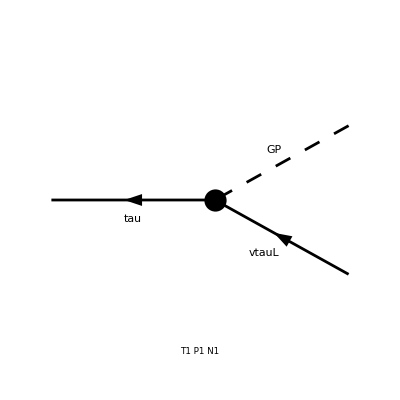

```mathematica
top3=CreateTopologies[0,1->2,Adjacencies->{3,4},ExcludeTopologies->{Internal,Tadpoles}];
ins3=InsertFields[top3,{-F[15]}->{S[3],-F[3]},Model->"Mine/1310.4838.LR",GenericModel->"Mine/1310.4838.LR",InsertionLevel->{Particles}];
Paint[ins3,ColumnsXRows->{3,1}];
```

```mathematica
<<tautauHW0gen_tree.res;
```

```mathematica
amp0
```

FeynAmpList[Process→{{F[6],p1,0,{-Q,LeptonNumber}},{-F[15],p2,0,{Q,-LeptonNumber}}}→{{-V[3],k1,0,{-Q}},{S[3],k2,MH,{Q}}},Model→{Mine/1310.4838.LR},GenericModel→{Mine/1310.4838.LR},AmplitudeLevel→{Particles},ExcludeParticles→{V,-F[7],F[7],-F[10],F[10],-F[7,{_}],F[7,{_}],-F[10,{_}],F[10,{_}],V[1],V[2],-V[3],V[3],V[4],V[5],V[4,{_}]},ExcludeFieldPoints→{FieldPoint[0][S[1],S[2],V[2]],FieldPoint[0][-S[3],S[3],V[2]]},LastSelections→{}][]